-Graphics-

# Statistical Distributions and Model Analysis

## Curve fitting

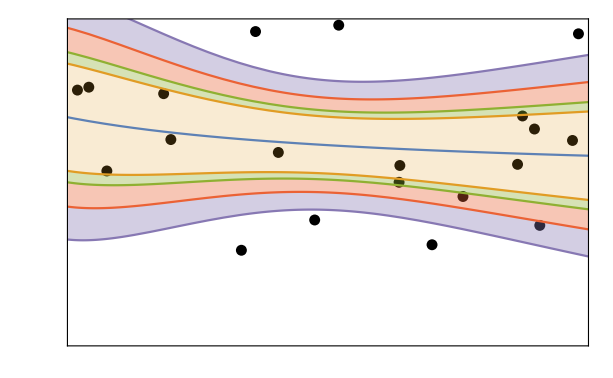

"Outline" |

### Webinar Part 1

Distribution Properties

Simulation of Distributions

Derived Distributions

Hypothesis Tests

Fitting Data to Distributions

Method of Moments Estimation

Bootstrapping & Confidence Estimation

### Webinar Part 2

Linear Model Fit

Nonlinear Model Fit

Fitting Theoretical Models

### Webinar Part 3

Generalized Linear Models

Piecewise Models

## Learning Objectives

The symbolic architecture of the Wolfram Language™ enables a uniquely convenient approach to working with statistical models. Starting from arbitrary data, the Wolfram Language is able to generate symbolic representations of fitted models, from which a full spectrum of results and diagnostics can immediately be extracted, visualized or used in other computations.

### Linear Model Fit

The function LinearModelFit uses linear regression to fit data to a linear function/model:

Data imputation: dealing with missing data

Data cleaning and fitting

Visualization and checking goodness of fit

Alternative models

### Nonlinear Model Fit

The NonlinearModelFit function can fit data with any given family of nonlinear functions:

Data cleaning and fitting

Visualization and checking goodness of fit

Robust regression for outliers

### Fitting Theoretical Models

Owing to the symbolic nature of the Wolfram Language, it is possible to fit theoretical models using parametric equations.

## Model Fitting: Terminology

Researchers from varied fields use statistics in their work. It is not uncommon for statistical concepts to have different names in different fields. Before proceeding, common terminology is introduced that will be used throughout this course:

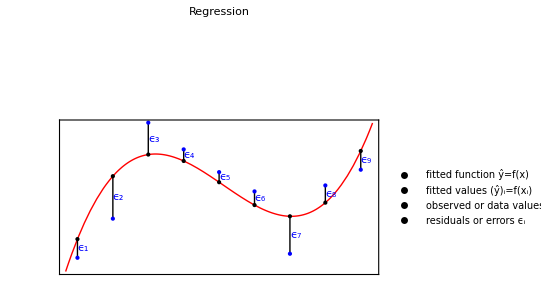

The independent variables x⃗={x_1,…,x_n}, the predictor variables. In the preceding diagram, x⃗ is a single variable.

The dependent variable: y, the response variable.

Model: the function and optimization criteria (e.g. distributional assumptions) used to approximate the behavior suggested by the data. A model will contain one or more parameters, to be determined by the fitting process.

Parameters: the values in the model that are not assumed by the predictor or response variables.

## Data Imputation

In statistics, imputation refers to the process of replacing missing data with substituted values. This allows for rectifying the disadvantages of deleting the entire row of data if a single value/data point is missing. This is especially useful when data is not easily available or collecting it is expensive.

There are various methods of single imputation. It will be demonstrated here with mean substitution. The file breamData.csv contains a subset of data about 159 fish taken from Lake Laengelmavesi in the early twentieth century. Begin by bringing the data into the Wolfram Language:

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
FileNames["*.csv"]
```

```mathematica
breamDat= Import["breamData.csv",{"CSV","Data"}];
```

```mathematica
Dataset[breamDat]
```

The first thing you notice is that the first column consists entirely of ones. You can also see there is an NA in the second column. Also, the last row does not seem to be consistent with the others:

```mathematica
breamDat[[-1]]
```

Eliminate the first column and last row and check the dimensions of the resulting set:

```mathematica
breamDat2= breamDat[[;;-2,2;;]];
```

```mathematica
Dimensions[breamDat2]
```

Get information about the NA seen in the file. It will either be a symbol or a string. Note how the Wolfram Language allows you to get several pieces of information at once:

```mathematica
{pos,#,Head[#]}&/@Extract[breamDat2,pos=Position[breamDat2,NA|"NA"]]
```

Get the information from the first and fourth columns and delete the row with the missing value:

```mathematica
fullRows=Delete[breamDat2[[All,{1,4}]],14]
```

Next, transpose the data to have it in column form and then divide the first column by the second:

```mathematica
cols=Transpose[fullRows]
```

```mathematica
rats=Apply[Divide,cols]
```

This gives an average scaling factor relating the L3 dimension to the weight:

```mathematica
mn=Mean[rats]
```

Replace the N/A in the fourteenth row with the scaled value of L3 in that row:

```mathematica
breamDat[[14,2]]=N@Round[mn breamDat2[[14,4]]]
```

```mathematica
breamDat
```

## Linear Models: Data Cleaning and Fitting

LinearModelFit produces a linear model of the form ŷ=β_0+β_1 f_1+β_2 f_2+… with given function ŷ and fitting parameters {β_0, β_1,…}, under the assumption that the original y_i are independent normally distributed with mean OverHat[y_i] and common standard deviation.

### Data Formatting

The file fishdata consists of information about a particular species of fish found in a lake in Finland. In this exercise, the relationship between the weight, the length and the thickness of the fish is investigated:

```mathematica
fishdata={{5.9,7.5,8.4,8.8,24.,16.},{32.,12.5,13.7,14.7,24.,13.6},{40.,13.8,15.,16.,23.9,15.2},{51.5,15.,16.2,17.2,26.7,15.3},{70.,15.7,17.4,18.5,24.8,15.9},{100.,16.2,18.,19.2,27.2,17.3},{78.,16.8,18.7,19.4,26.8,16.1},{80.,17.2,19.,20.2,27.9,15.1},{85.,17.8,19.6,20.8,24.7,14.6},{85.,18.2,20.,21.,24.2,13.2},{110.,19.,21.,22.5,25.3,15.8},{115.,19.,21.,22.5,26.3,14.7},{125.,19.,21.,22.5,25.3,16.3},{130.,19.3,21.3,22.8,28.,15.5},{120.,20.,22.,23.5,26.,14.5},{120.,20.,22.,23.5,24.,15.},{130.,20.,22.,23.5,26.,15.},{135.,20.,22.,23.5,25.,15.},{110.,20.,22.,23.5,23.5,17.},{130.,20.5,22.5,24.,24.4,15.1},{150.,20.5,22.5,24.,28.3,15.1},{145.,20.7,22.7,24.2,24.6,15.},{150.,21.,23.,24.5,21.3,14.8},{170.,21.5,23.5,25.,25.1,14.9},{225.,22.,24.,25.5,28.6,14.6},{145.,22.,24.,25.5,25.,15.},{188.,22.6,24.6,26.2,25.7,15.9},{180.,23.,25.,26.5,24.3,13.9},{197.,23.5,25.6,27.,24.3,15.7},{218.,25.,26.5,28.,25.6,14.8},{300.,25.2,27.3,28.7,29.,17.9},{260.,25.4,27.5,28.9,24.8,15.},{265.,25.4,27.5,28.9,24.4,15.},{250.,25.4,27.5,28.9,25.2,15.8},{250.,25.9,28.,29.4,26.6,14.3},{300.,26.9,28.7,30.1,25.2,15.4},{320.,27.8,30.,31.6,24.1,15.1},{514.,30.5,32.8,34.,29.5,17.7},{556.,32.,34.5,36.5,28.1,17.5},{840.,32.5,35.,37.3,30.8,20.9},{685.,34.,36.5,39.,27.9,17.6},{700.,34.,36.,38.3,27.7,17.6},{700.,34.5,37.,39.4,27.5,15.9},{690.,34.6,37.,39.3,26.9,16.2},{900.,36.5,39.,41.4,26.9,18.1},{650.,36.5,39.,41.4,26.9,14.5},{820.,36.6,39.,41.3,30.1,17.8},{850.,36.9,40.,42.3,28.2,16.8},{900.,37.,40.,42.5,27.6,17.},{1015.,37.,40.,42.4,29.2,17.6},{820.,37.1,40.,42.5,26.2,15.6},{1100.,39.,42.,44.6,28.7,15.4},{1000.,39.8,43.,45.2,26.4,16.1},{1100.,40.1,43.,45.5,27.5,16.3},{1000.,40.2,43.5,46.,27.4,17.7},{1000.,41.1,44.,46.6,26.8,16.3}};
```

The columns in fishdata are weight, length 1, length 2, length 3, height and thickness. The objective is to estimate the weight of a fish from its physical dimensions, so it is best to put the weight in the last column. The height and the thickness are given as a percent of the third length, L3, so you need to compute its absolute value:

```mathematica
wrkDat=fishdata/.{{wt_,L1_,L2_,L3_,ht_,thk_}:> {L1,L2,L3,ht L3/100,thk L3/100,wt}};
```

Begin by looking at the weight as a function of the L3 value:

```mathematica
ListPlot[wrkDat[[All,{3,-1}]]]
```

### Fitting the Data

```mathematica
?LinearModelFit
```

This fits the data to a cubic polynomial. Give the fitted model a name for use in subsequent investigations:

```mathematica
wtEst1=LinearModelFit[wrkDat[[All,{3,-1}]],x^Range[1,3],x]
```

Visualize the fit:

```mathematica
Plot[wtEst1[x],{x,8,48},Epilog-> {Point[wrkDat[[All,{3,-1}]]]}]
```

## Linear Models: Getting Information about the Fit

The FittedModel object contains a lot of additional information on the details of the fit. Use "Properties" as an argument to get the properties as a list:

```mathematica
Framed[NiceTable[Style[#,14,"Text"]&/@wtEst1["Properties"]],RoundingRadius-> 12,FrameMargins-> 15]
```

Obtain a single property or a list of properties from the fit. Look at the ANOVA table and adjusted R-squared values for your fit:

```mathematica
wtEst1[{"ANOVATable","AdjustedRSquared"}]
```

Visualize the fit with mean prediction bands:

```mathematica
With[{expr= Join[{wtEst1[x]},wtEst1["MeanPredictionBands"]]},Plot[expr,{x,8,48},Epilog-> {Point[wrkDat[[All,{3,-1}]]]},Filling-> {2-> {3}}]]
```

## Linear Models: Alternate Models

So far, a single predictor variable, length 3, has been selected to model the weight of the fish. Adding further predictor variables could, however, improve the fit. Now the full dataset will be used to give a select set of basis vectors for the model.

Start with the same model as before, using only length 3, but the full dataset:

```mathematica
wtEst2=LinearModelFit[wrkDat,L3^Range[0,3],{L1,L2,L3,Ht,Thck}]
```

Note the only difference is the way in which you ask for the result:

```mathematica
Column[{wtEst1[L3],wtEst2[L1,L2,L3,Ht,Thck]}]
```

Using the information from the previous slide, you can fit several models at the same time using the Table function:

```mathematica
multiFit=Table[LinearModelFit[wrkDat,basis,{L1,L2,L3,Ht,Thck}],{basis,{L3^Range[1,3],(*powers of length 3*){L3,Ht},(*length 3 and height*){L3,Thck},(*length 3 and thickness*)Flatten[{L3,L3^2,Ht}]}}] (*some powers of length 3 and height*)
```

The last model in the list accounts for up to 98% of the variation in the weights of the fish. The AIC of all the fits can also be compared:

```mathematica
Through[multiFit["AdjustedRSquared"]]
```

```mathematica
Through[multiFit["AIC"]]
```

Here are ANOVA tables for the first and last models in your set:

```mathematica
Through[multiFit[[{1,-1}]]["ANOVATable"]]
```

Here is a visualization of the last model in the list:

```mathematica
Show[{Plot3D[Through[multiFit[[{-1}]][0,0,L3,Ht,0]],{L3,8,48},{Ht,2,13}],Graphics3D[ {Black,PointSize[Medium],Point[wrkDat[[All,{3,4,6}]]]}]}]
```

Having decided on a model, simplify things by constructing a model using only the necessary variables:

```mathematica
wtEst3= LinearModelFit[wrkDat[[All,{3,4,6}]],Flatten[{L3^Range[0,2],Ht}],{L3,Ht}]
```

```mathematica
ListPlot[wtEst3["FitResiduals"]]
```

## Nonlinear Model Fit: Data Cleaning

Linear models are fitted using linear algebra, a process that is, in most cases, robust and fast. Nonlinear models, on the other hand, require the construction of a merit function and then minimizing the merit function based on varying a set of parameters present in the model. This process can be slow and often requires more attention on the part of the statistician.

In this example, a file that contains data on yearly production from different sources of energy will be imported. Look at the renewable energy sources and try to find a relationship that defines the growth in the production of renewable sources over time:

```mathematica
electricData= Import[FileNameJoin[{NotebookDirectory[],"epmxlfile1_1.xls"}],{"Data",1}];
Dimensions[electricData]
```

Here you can look at renewables up through the year 2010. First, determine the number of the columns containing the data you want to use. The information of interest is in the ninth column:

```mathematica
Position[electricData,"Other Renewables[4]"]
```

Referring to the preceding table, select rows 4 through 57 and columns 1 and 9:

```mathematica
renewables=electricData[[4;;57,{1,9}]];
```

Using pattern matching, convert the strings to numbers and extract only the yearly totals:

```mathematica
yearTots=Cases[renewables,{_?NumericQ|"Total",_?NumericQ}];
```

Using replacement rules, “clean up” the rows corresponding to the years 2006, 2007 and 2008:

```mathematica
elecdata=ReplacePart[yearTots,{{-3,1}-> 2006.,{-2,1}->2007.,{-1,1}->2008.}];
```

## Nonlinear Model Fit: Data Fitting

Now that you have cleaned up the data, you can look at the form of the data and determine a model. Apart from the year 2001, this looks a lot like exponential growth:

```mathematica
ListPlot[elecdata,Mesh-> All]
```

Use NonlinearModelFit to see if this gives a reasonable fit to the data. Note the translation of the variable by c, to get the curve to fit. Raising ⅇ to a large power is going to give misleading information:

```mathematica
Clear[a,b,c,t]
```

```mathematica
model=NonlinearModelFit[elecdata,a+ⅇ^(b (t-c)),{a,b,{c,1990}},t]
```

```mathematica
model["BestFit"]
```

The fit appears to be a good one:

```mathematica
Show[
Plot[model[t],{t,1993.5,2008.5},PlotStyle->{Pink,Thick},PlotRange->All],
ListLinePlot[elecdata,Mesh-> All,PlotMarkers-> Automatic]
]
```

The property list for NonlinearModelFit:

```mathematica
NiceTable[Style[#,12,"Text"]&/@model["Properties"]]
```

```mathematica
model[{"ANOVATable","FitCurvatureTable","ParameterBias","AICc"}]
```

## Nonlinear Model Fit: Weights

In this form of regression, outliers will be dealt with.The value for the year 2001 in the data seems inconsistent with the rest of the values; it could have been recorded incorrectly, or it could be an outlier. In either case, you might want to use robust regression to reduce the influence of that observation on the fit. That is done in NonlinearModelFit using the option Weights:

```mathematica
errors=ConstantArray[0.1,Length[elecdata]];errors[[8]]=0.5;
```

```mathematica
model2=NonlinearModelFit[elecdata,a+ⅇ^(b (t-c)),{a,b,{c,1990}},t,Weights-> 1/errors^2,VarianceEstimatorFunction->(1&)];
```

```mathematica
GraphicsRow[{Show[
{Plot[model[t],{t,1993.5,2008.5},PlotStyle->{Orange,Thick},PlotRange->All],
ListLinePlot[elecdata,Mesh-> All,PlotMarkers-> Automatic]},PlotLabel-> Style["model",14,Bold]
],Show[{
Plot[model2[t],{t,1993.5,2008.5},PlotStyle->{Orange,Thick},PlotRange->All],
ListLinePlot[elecdata,Mesh-> All,PlotMarkers-> Automatic]},PlotLabel-> Style["model2",14,Bold]
],Plot[{model2[t]-model[t]},{t,1993.5,2008.5},PlotStyle->{Orange,Thick},PlotRange->All,PlotLabel-> Style["model2-model",14,Bold]]},ImageSize-> 12 72]
```

## Fitting Theoretical Models

In many disciplines—science and engineering, for example—you need to test theoretical models. The Wolfram Language provides a very nice framework for this task. For example, a first-order approximation to the velocity of a rocket at time t should satisfy the solution to the differential equation

dv/dt=(β s)/(m_0−β t)−g,
v_0=0

where g is acceleration due to gravity, m_0 is initial mass, s is exhaust velocity and β is fuel consumption.

This model has a symbolic solution, so you could take that approach, but more sophisticated models may not have a symbolic solution. You can illustrate that situation and assume there is no symbolic solution available. Confidence is assumed for estimates of all the parameters except for β. You can attempt to estimate β from observed (in this case simulated) data.

Bring in your data:

```mathematica
FileNames["*.dat"]
```

```mathematica
rcktDat= Import["rcktDat.dat"];
```

```mathematica
Dimensions[rcktDat]
```

```mathematica
InputForm/@rcktDat[[;;3]]
```

```mathematica
rcktDat=Flatten[rcktDat/.{str_String:> ToExpression@StringSplit[str,","]},1]
```

Begin by creating a ParametricFunction:

```mathematica
sol=ParametricNDSolve[{v'[t]==-9.8+(700 β)/(10000-t β),v[0]==0},v,{t,0,60},{β}]
```

Use the parametric function in NonlinearModelFit. Note the positions of the parameter β and the variable t:

```mathematica
rcktModl=Quiet[NonlinearModelFit[Most[rcktDat],v[β][t]/.sol,{β},t]]
```

Visualize the results:

```mathematica
Plot[rcktModl[t],{t,0,60},Epilog-> Point[rcktDat]]
```

As with any fit, you should look at the diagnostics. Even though you have obtained your solution using interpolating functions, you still have diagnostics available from the fit:

```mathematica
rcktModl["ANOVATable"]
```

```mathematica
rcktModl[{"ParameterTable","ParameterBias"}]
```

```mathematica
ListPlot[rcktModl["FitResiduals"],Filling-> Axis]
```

```mathematica
Clear[rcktModl,rcktDat]
```

## Glossary

AdjustedRSquared | AIC | AICc | All | ANOVATable
Apply | BestFit | Cases | Column | ConstantArray
Dataset | Delete | Dimensions | Divide | Epilog
Extract | FileNames | Filling | First | FitCurvatureTable
FitResiduals | Flatten | Framed | FrameMargins | GatherBy
Graphics3D | GraphicsRow | Head | ImageSize | Import
Join | Length | LinearModelFit | ListLinePlot | ListPlot
Map | Mean | MeanPredictionBands | Medium | Mesh
Most | N | NonlinearModelFit | NotebookDirectory | NumericQ
ParameterBias | ParametricNDSolve | Plot3D | PlotMarkers | PlotRange
PlotStyle | Point | PointSize | Position | Quiet
ReplaceAll | ReplacePart | Round | RoundingRadius | SetDirectory
Short | Show | StringSplit | Style | Table
Through | ToExpression | Transpose | VarianceEstimatorFunction | Weights
With |  |  |  |

## Review Exercises

#### Provided Separately

## Initialize Cells

```mathematica
NiceTable[lis_List,opts:OptionsPattern[Grid]]:= Grid[Partition[lis,4,4,{1,-1},""],{opts,Alignment-> Left}]
```